## Using the KNN method to diagnose breast cancer tumours

## Assessed practical

Please read:

This is an assessed practical. Marks are indicated for each task. The maximum is 45 marks.

Complete your answers below each question within this notebook (similar to what I did for the answers of practical 1 and 2). Indicate how you get to your answers. Marks can be discounted if it is not clear how you obtained the results.

This is supposed to be completed individually. Signs of plagiarism may lead to discounted marks.

Upload your notebook with answers to the assessment page in MyAberdeen by Friday 20 November at 23:00 GMT.

You may want to ask questions to the course coordinator or tutor but please note that help will obviously be much more limited than for a normal non-assessed practical.

## Objective

This main objective of this practical is to train classifiers to diagnose cancer into benign and malignant classes using morphological features of tumours.

Features are computed from a digitized image of a fine needle aspirate (FNA) of a breast mass. They describe characteristics of the cell nuclei present in the image.

## The data

The breast cancer data includes 569 examples of cancer biopsies, each with 32 features. One feature is an identification number, another is the cancer diagnosis, and 30 are numeric-valued laboratory measurements. The diagnosis is coded as M to indicate malignant or B to indicate benign.

The 30 numeric measurements comprise the mean, standard error, and worst (that is, largest) value for 10 different characteristics of the digitized cell nuclei.

## Task 1 [0 mark, just getting familiar with the data]

Before downloading the data, import additional information on the data from the site

https://archive.ics.uci.edu/ml/machine-learning-databases/breast-cancer-wisconsin/wdbc.names

In particular, look at the description of the Attribute information item which describes the columns of the data. It defines the 10 different characteristics of the sample.

```mathematica
Import["https://archive.ics.uci.edu/ml/machine-learning-databases/breast-cancer-wisconsin/wdbc.names"];
```

Check that the description agrees with the following meaning for the columns of the data:

```mathematica
colnames={"id","diagnosis","radius_mean","texture_mean","perimeter_mean","area_mean","smoothness_mean","compactness_mean","concavity_mean","concave points_mean","symmetry_mean","fractal_dimension_mean","radius_se","texture_se","perimeter_se","area_se","smoothness_se","compactness_se","concavity_se","concave points_se","symmetry_se","fractal_dimension_se","radius_worst","texture_worst","perimeter_worst","area_worst","smoothness_worst","compactness_worst","concavity_worst","concave points_worst","symmetry_worst","fractal_dimension_worst"};
```

```mathematica
Length[colnames]
```

32

## Task 2 [1 mark]

Import the data using the following link:

https://archive.ics.uci.edu/ml/machine-learning-databases/breast-cancer-wisconsin/wdbc.data

Assign the imported data to a variable, say data1

```mathematica
data1 =Import["https://archive.ics.uci.edu/ml/machine-learning-databases/breast-cancer-wisconsin/wdbc.data"] ;
```

## Task 3 [1 marks]

Check that the dataset data1 consists of 32 columns and 569 lines (rows). Columns correspond to the features of each sample (or instance) and there is a line for each sample. Show how you did it (otherwise, the question will be marked as 0)

```mathematica
(*Check Dimensions, Empty elements and view in table form to see line for each sample*)
```

```mathematica
Dimensions[data1]
```

{569,32}

```mathematica
Position[data1,{}]
```

{}

```mathematica
check = data1 // TableForm;
```

## Task 4 [2 marks]

Diagnosis is the variable we want to predict.

Define a variable named diagnosis from a sublist of data1. Check that elements in this list take values “B” (benign) or “M” (malignant) [1 mark]

Check that 357 samples are benign (B) and 212 are malignant (M) [1 mark]

```mathematica
type = DeleteDuplicates[data1[[All,2]]]
```

{M,B}

```mathematica
diagnosis = Cases[data1, {___, #, ___}] &/@ type;
```

```mathematica
Length[diagnosis]
```

2

```mathematica
diagnosis[[1]] // Length
```

212

```mathematica
diagnosis[[2]] // Length
```

357

```mathematica
(*Other method*)
```

```mathematica
M = data1[[Flatten[Position[data1[[ ;;, 2]], "M"]]]];
```

```mathematica
Flatten[Position[data1[[;;,2]],"M"]];
```

```mathematica
Table[i,{i,Length[data1]}];
```

```mathematica
B=data1[[Complement[Table[i,{i,Length[data1]}],Flatten[Position[data1[[;;,2]],"M"]]]]];
```

```mathematica
Length[M]
```

212

```mathematica
Length[B]
```

357

## Task 5 [2 marks]

Define an object called numericfeatures containing the numerical features from data1 describing the morphology of tumours for all the samples. [1 mark]

```mathematica
numericfeatures = data1[[All;;, 3;;32]];
```

For later analysis (e.g. Task 6), it is also useful to define a list of names from the numerical features (only for numerical features). You may refer to this list as numericnames.[1 mark]

```mathematica
numericnames = {"radius_mean","texture_mean","perimeter_mean","area_mean","smoothness_mean","compactness_mean","concavity_mean","concave points_mean","symmetry_mean","fractal_dimension_mean","radius_se","texture_se","perimeter_se","area_se","smoothness_se","compactness_se","concavity_se","concave points_se","symmetry_se","fractal_dimension_se","radius_worst","texture_worst","perimeter_worst","area_worst","smoothness_worst","compactness_worst","concavity_worst","concave points_worst","symmetry_worst","fractal_dimension_worst"};
```

```mathematica
(* We will use m1 & m2 to manipulate numeric names list, that will be defined in task6, so for right now i will make a new varaible and set it equal to 1 to test that the right index is called*)
```

```mathematica
t =1;
```

```mathematica
numericnames[[t]]
```

radius_mean

## Task 6 [2 marks]

Plot the scatter plot matrix for the features giving the mean values of the morphological features in the data set (remember that mean values of morphological features are only a subset of the features in the list numericfeatures.)

```mathematica
(*testing to plot two features first*)
```

```mathematica
m1 =1;
m2 =2;
```

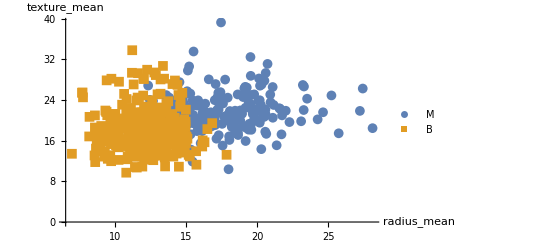

```mathematica
ListPlot[{diagnosis[[1]][[All, {m1+2 ,m2+2}]], diagnosis [[2]][[All, {m1+2 ,m2+2}]]}, AxesLabel-> numericnames[[{m1 ,m2}]], PlotLegends -> type, PlotMarkers -> {Automatic, Medium}]
```

```mathematica
(*now we will compare all the mean values*)
```

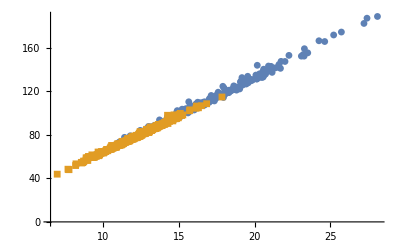
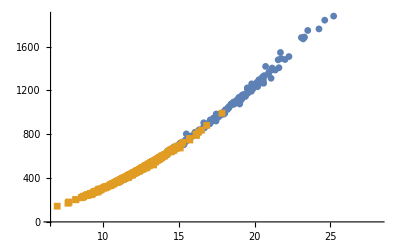
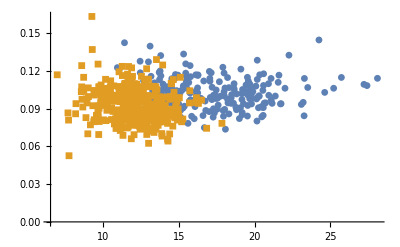
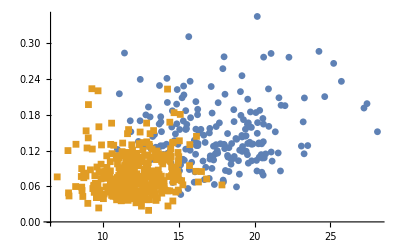
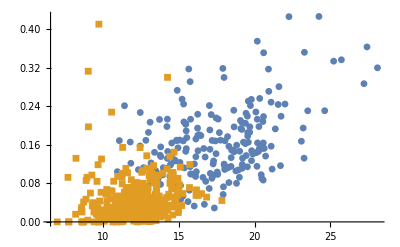
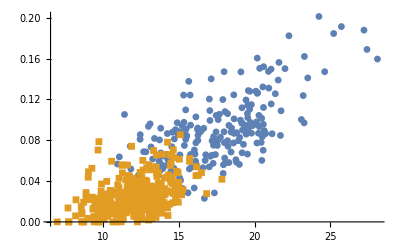
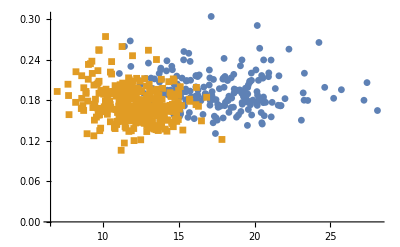
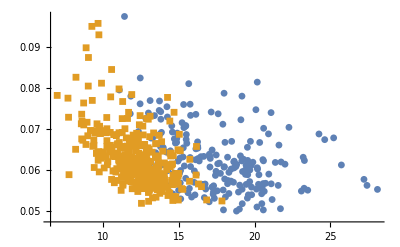
radius_mean | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | texture_mean | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | perimeter_mean | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | area_mean | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | smoothness_mean | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | compactness_mean | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | concavity_mean | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | concave points_mean | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | symmetry_mean | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | fractal_dimension_mean

```mathematica
Table[ If[i ==j, numericnames[[i]], ListPlot[{diagnosis[[1]][[All, {i +2, j+3}]], diagnosis[[2]][[All, {i +2, j+3}]]}, PlotMarkers ->{Automatic, Small}]], {i, 10}, {j, 10}] //Grid
```

## Task 7 [1 mark]

Based on the scatter plot matrix obtained in the in Task 6, do you think different classes are separated enough as for classification to be successful?

```mathematica
(*Based on the scatter plot matrix we can say that most instances are separated enough,the measurements cluster by diagnosis,however,there are a couple instances where the cluster is not clear.Most of them are clear so there is hope a good classification of diagnosis type for unseen samples.*)
```

## Task 8 [2 marks]

Proceed as usual by defining test and training datasets that will be used to train and test a classifier, respectively. 

We will use the first 300 records for the training dataset and the remaining 269 to simulate new patients. Refer to the training and test datasets as trainingSet and testSet, respectively.

```mathematica
trainingSet = Take[numericfeatures, 300];
testSet = Take[numericfeatures, 301 ;;];
```

```mathematica
Length[trainingSet]
```

300

```mathematica
Length[testSet]
```

269

```mathematica
Intersection[testSet, trainingSet]
```

{}

## Task 9 [2 marks]

When we constructed our training and test data, we excluded the target variable, diagnosis. However, we will need them for training the KNN model. Store the class labels for the training and test datasets in lists named trainLabels and testLabels.
[2 marks]

```mathematica
trainLabels = data1[[;;300, 2]] ;
```

```mathematica
testLabels = data1[[301 ;;-1, 2]] ;
```

```mathematica
Length[trainLabels]
```

300

```mathematica
Length[testLabels]
```

269

## Task 10 [1 mark]

As explained in lectures, the KNN method works best for balanced training datasets (i.e. not biased). Check that bias in the training dataset is minimal.

```mathematica
Tally[trainLabels]
```

{{M,146},{B,154}}

```mathematica
(*we can see that there is no bias in the training dataset as both the diagnosis are nearly equal with there instances in our training dataset*)
```

## Task 11 [2 marks]

Use the lists trainingSet and trainLabels to train a classifier using the Nearest Neighbors method with k = 15 neighbours

```mathematica
k = 15;
```

```mathematica
cf = Classify[trainingSet -> trainLabels, Method -> {"NearestNeighbors", "NeighborsNumber" -> k}]
```

ClassifierFunction[…]

## Task 12 [2 mark]

In order to test the performance of the trained classifier, use the testSet and testLabels lists to generate a ClassifierMeasurements object.

```mathematica
assc = Table[testSet[[i, 1;;30]] ->  testLabels[[i]], {i , 1, Length[testSet]}];
```

```mathematica
cm = ClassifierMeasurements[cf, assc]
```

ClassifierMeasurementsObject[…]

## Task 13 [10 marks]

Check the accuracy, error, FPR, FNR, confusion matrix and ROC curves of the classifier. [3 marks]
Comment on the results. [7 marks]

```mathematica
cm["Accuracy"]
```

0.973978

```mathematica
cm["Error"]
```

0.0260223

```mathematica
cm["FalsePositiveRate"]
```

<|B→0.0151515,M→0.0295567|>

```mathematica
cm["FalseNegativeRate"]
```

<|B→0.0295567,M→0.0151515|>

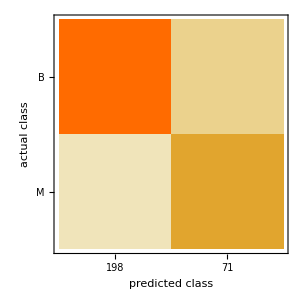

```mathematica
cm["ConfusionMatrixPlot"]
```

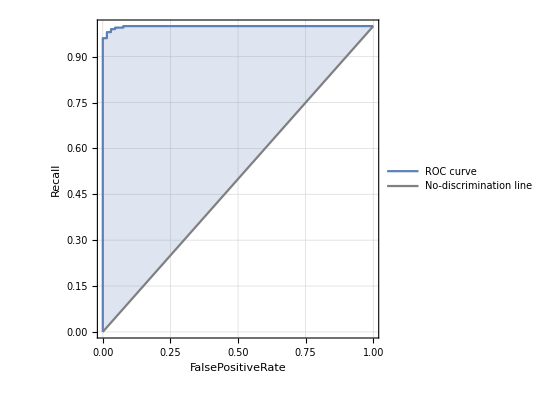
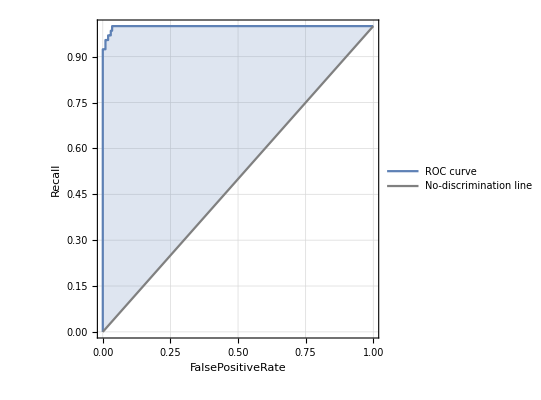
<|B→-Graphics-,M→-Graphics-|>

```mathematica
cm["ROCCurve"]
```

```mathematica
(* From the results we can see the the classification is very accurate, with an accuracy of  97.39% and error of 2.60%. From the FPR & FNR, we can conclude they the classifier did a good job, as both are extremely low, FPR being 1.5% for B and 2.9% for M and FNR being 2.9% for B and 1.5% for M. From the FPR and FNR we can see that the diagnosis M does better than B by around 1.5% for both FNR and FPR, this is clear as only one example of M was missclassified as B where as 6 examples of B were missclassified as M, . The Confusion Matrix shows us that the classifer got 262 classes correct and only 7 incorrect. We can conclude that the classifier has a harder time predicting M, as it got 6 instances mixed up as B, while it only once classified M incorrectly. The ROC cruves suggest that the classification of diagnosis B is more precise. *)
```

## Task 14 [4 marks]

As you probably already guessed, in a problem as serious as cancer, it is important that malignant tumours are classified as malignant with high probability. Calculate the percentage of malignant tumours in the test dataset that are classified as malignant with probability larger than 0.95.

```mathematica
Tally[testLabels];
```

```mathematica
prob = SortBy[Transpose[{testLabels, cm ["Probabilities"]}], First];
```

```mathematica
prob= Cases[prob, { #, ___}] &/@ type;
```

```mathematica
ms= prob[[1]];
```

```mathematica
over95 =Count[ms[[All;;,2]], x_/; x>0.95];
```

```mathematica
total =Length[ms]
```

66

```mathematica
mprob95 = (over95/total) // N
```

0.787879

```mathematica
(* 78.79% of of malignant tumours in the test dataset are classified as malignant with probability larger than 0.95*)
```

## Task 15 [5 marks]

In lectures, it was demonstrated that the number of neighbours used for the KNN method may significantly influence the error of a classifier. Systematically study the error of the classifier trained in Task 12 as a function of the number of neighbours k (you may want to do this by adapting the error[k] function proposed in the lecture on the KNN method to the current problem). Plot the error of the classifier as a function of k. Discuss the result, including a discussion on whether choosing k = 15 in task 11 was appropriate.
[5 marks]

```mathematica
error[k0_,trainset_,testset_]:=Module[{k=k0,cf,trainLabels= trainset,cm,assc = testset},
cf= Classify[trainingSet -> trainLabels, Method -> {"NearestNeighbors", "NeighborsNumber" -> k}];
cm=ClassifierMeasurements[cf,assc];
cm["Error"]
]
```

```mathematica
error[15, trainLabels, assc]
```

0.0260223

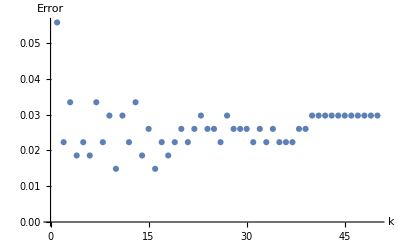

```mathematica
plot50 = ListPlot[Table[{k,error[k,trainLabels,assc]},{k,1,50, 1}],PlotRange->All,AxesLabel->{"k","Error"}]
```

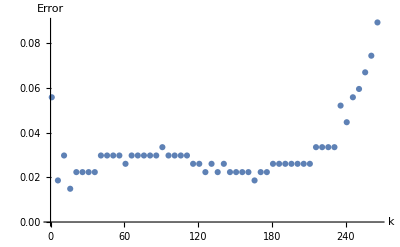

```mathematica
plot269 = ListPlot[Table[{k,error[k,trainLabels,assc]},{k,1,269, 5}],PlotRange->All,AxesLabel->{"k","Error"}]
```

```mathematica
error[10, trainLabels, assc]
```

0.0148699

```mathematica
(*From the graph and error function, it seems that k= 15 was appropriate, however, not the best value given the paramters. I calcualted that when k=10, we get he lowest error of 1.49%. This does not mean that 15 was a innapppriate value, as we can see any value ranging from 2 - 170 seems to be appropriate based on the graph, however, the value 1 and the range from 170- 269 seem to have the worst error.*)
```

## Task 16 [8 marks]

In some cases, one can identify features in datasets that are easy to predict as a function of other features, i.e. features that are closely related to each other with a small dispersion. Using several features that are very much related to each other might not improve the performance of the classifier significantly. For instance, using a feature with value x would give the same classification power as using three features with values x, 2x and x^2. Indeed, the features with values 2x and x^2 would not bring additional information to the classification. Following this observation, it might make sense to drop features that are highly predictable in terms of other features and check how the performance of a classifier is affected. The idea is that this might help fighting against the curse of dimensionality.

In order to check this for the breast cancer dataset, do the following:

Observe the scatter plot matrix obtained in Task 6 and suggest some morphological features that can be easily predicted in terms of other features. [2 marks]

```mathematica
(* We will visually inspect the scatter plots, each feature has its own column and row so we will inspect both for every single feature. We will be looking for features that have a small dispersion, indicating that they are closely related to each other, features that overlap. From the visual inspection we can conclude that "Smoothness", "Symmetry" and "Fractional Dimensions" are features that are easy to predict as fucntion of other functions so those will be removed. Both the mean, standard error and worst column will be removed for every feature. In all my work above, I had already removed ID as it was redundant, however, I am just stating this incase it was not clear.*)
```

Redefine the trainingSet and testSet (see Task 8) by dropping potentially redundant features from the list numericfeatures. [2 mark]

```mathematica
(*We are dropping the columns of the redundant features from the numeric features list, those include the mean, standard error and worse of smoothness, symmetry and fractional dimensions*)
```

```mathematica
dropColumns[mat_?MatrixQ,columns:{__Integer}]:=With[{columnsToTake=Complement[Range[Dimensions[mat][[2]]],columns]},mat[[All,columnsToTake]]];
```

```mathematica
redtrainingSet = dropColumns[trainingSet,{5,9,10,15,19,20,25,29,30}];
```

```mathematica
redtestSet = dropColumns[testSet,{5,9,10,15,19,20,25,29,30}];
```

Train a KNN classifier with k = 15 for the new training dataset. [0.5 marks]

```mathematica
(*Training a KNN classifier just like we did above, K is already set above. I named the classifer redcf (redefined clasifier to make it easier for me to run and test in notebook)*)
```

```mathematica
redcf = Classify[redtrainingSet -> trainLabels, Method -> {"NearestNeighbors", "NeighborsNumber" -> k}]
```

ClassifierFunction[…]

Use the new test dataset to obtain a ClassifierMeasurements object and explore the error and confusion matrix. [1.5 marks]

Discuss whether dropping the potentially redundant features affected the performance of the classifier? [2 mark]

```mathematica
assc1 = Table[redtestSet[[i, 1;;21]] ->  testLabels[[i]], {i , 1, Length[redtestSet]}];
```

```mathematica
redcm = ClassifierMeasurements[redcf, assc1]
```

ClassifierMeasurementsObject[…]

```mathematica
redcm["Error"]
```

0.0260223

```mathematica
cm["Error"]
```

0.0260223

```mathematica
redcm["Accuracy"] && cm ["Accuracy"]
```

0.973978&&0.973978

```mathematica
(*We can see that dropping the potentailly redudant features has no effect on the accuracy or error percentage of the classifer as the new and redefined hold the same percentages. However the confusion matrixes do seem a little different*)
```

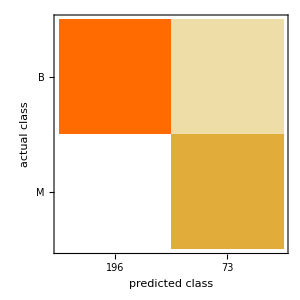
-Graphics-&&-Graphics-

```mathematica
redcm["ConfusionMatrixPlot"]&&cm["ConfusionMatrixPlot"]
```

```mathematica
redcm["FalsePositiveRate"]
```

<|B→0.,M→0.0344828|>

```mathematica
cm["FalsePositiveRate"]
```

<|B→0.0151515,M→0.0295567|>

```mathematica
redcm["FalseNegativeRate"]
```

<|B→0.0344828,M→0.|>

```mathematica
cm["FalseNegativeRate"]
```

<|B→0.0295567,M→0.0151515|>

```mathematica
(* When comapring both the confusion matrixes we are able to conclude that our new classifer has a 100% precision of predicting class B, which is a 0.5% improvement from before, however has a precision of 90% of predicting class M, which is 1.5% decrease compared to our previous classifer. That is clear when comparing the FNR and FPR of both classifiers. The new classifer has a harder time, classifying the M diagnosis, as it incorrectly predicts 7 instances as being part of the B class.*)

(*Since dropping the redundant features didn't prove to make a big difference, I tested wether removing key features that clearly vary based on the daignosis from each other, would make a difference. I removed features (all three instances of each) of texture, paramter and area and here are my results*)
```

```mathematica
badtrainingSet = dropColumns[trainingSet,{2,3,4,12,13,14,22,23,24}];
```

```mathematica
badtestSet = dropColumns[testSet,{2,3,4,12,13,14,22,23,24}];
```

```mathematica
badcf = Classify[badtrainingSet -> trainLabels, Method -> {"NearestNeighbors", "NeighborsNumber" -> k}];
```

```mathematica
badassc = Table[badtestSet[[i, 1;;21]] ->  testLabels[[i]], {i , 1, Length[redtestSet]}];
```

```mathematica
testcm = ClassifierMeasurements[badcf, badassc];
```

```mathematica
testcm["Error"]
```

0.0371747

```mathematica
testcm["Accuracy"]
```

0.962825

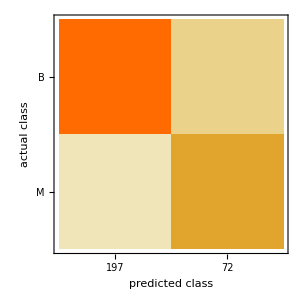
-Graphics- -Graphics-

```mathematica
testcm["ConfusionMatrixPlot"]  cm["ConfusionMatrixPlot"]
```

```mathematica
(* From these results, we can say that removing key features from the training and testing data do make a difference. As we can see the Error percentage has gone up to 3.7% along with the Accuracy percentage going down to 96.3% compared to the original of 2.6% and 97.4%. *)
(* In conclusion, removing redundant features only impacts our classifier to very minimal levels. The Accuracy and Error is equal with the only differenece being in the FPR and FNR values. This would be useful if we needed the daignosis of M to be classified with greater precision, however, it would lead to more diagnosis of M being falsely predicted too, which isnt good, especially with something as serious as cancer. Removing redundant features could be useful in decrease FPR and FNR values and vice versa, depending on the scenario and type of data. We can also conclude that removing important classification features, in other words non redundant features proves hurtful to our classifier as the accuracy suffers. *)
```